```mathematica
ClearAll["Global`*"]
```

```mathematica
rhorcb=Matm gamma/(gamma-1)1/(4 Pi Rc^2 Rrcb) (Rc^2 /(Rbp Rrcb))^(1/(gamma-1))
```

(gamma Matm (Rc^2/(Rbp Rrcb))^(1/(-1+gamma)))/(4 (-1+gamma) π Rc^2 Rrcb)

```mathematica
En=-G Mc/Rc^2 Rrcb (gamma/(2 gamma-1) Matm + 1/gamma (gamma-1)/(gammac-1) mu/muc Mc)
```

-(G Mc ((gamma Matm)/(-1+2 gamma)+((-1+gamma) Mc mu)/(gamma (-1+gammac) muc)) Rrcb)/Rc^2

```mathematica
L= 64 Pi/3 sigma Trcb^4 Rbp/(kappa rhorcb)
```

(256 (-1+gamma) π^2 Rbp Rc^2 (Rc^2/(Rbp Rrcb))^(-1/(-1+gamma)) Rrcb sigma Trcb^4)/(3 gamma kappa Matm)

```mathematica
(*Trcb=(gamma-1)/gamma G Mc mu/kb Rc/(Rbp Rrcb)*)
```

(G (-1+gamma) Mc mu Rc)/(gamma kb Rbp Rrcb)

```mathematica
time=-En/L
```

(3 gamma^5 kappa kb^4 Matm ((gamma Matm)/(-1+2 gamma)+((-1+gamma) Mc mu)/(gamma (-1+gammac) muc)) Rbp^3 (Rc^2/(Rbp Rrcb))^(1/(-1+gamma)))/(256 G^3 (-1+gamma)^5 Mc^3 mu^4 π^2 Rc^4 sigma)

```mathematica
Rrcb=Rbp;
```

```mathematica
sol=Solve[time==t, Matm];
```

```mathematica
Matm=Matm/.sol[[2]]
```

(16 A G^(3/2) √(3-2 gamma) (-1+gamma) Mc^(3/2) mu^2 π (Rbp/Rc)^(-(4-3 gamma)/(2 (-1+gamma))) √Rc √sigma √t)/(√3 gamma^(3/2) √kappa kb^2)

```mathematica
L
```

(16 G^(5/2) (-1+gamma)^3 Mc^(5/2) mu^2 π (Rbp/Rc)^((4-3 gamma)/(2 (-1+gamma))) √sigma)/(√3 √(3-2 gamma) gamma^(5/2) √kappa kb^2 √Rc √t)

```mathematica
mp=1.67*^-24;
G=6.67*^-8;
sigma=5.67*^-5;
Me=6*^27;
kb=1.38*^-16;
yr=365*24*3600;
```

```mathematica
mu=2.35 mp;
Td=1000;
rhoc=2;
kappa=0.1;
gamma=7/5;
Mc=10 Me;
Rbp= G Mc mu/(kb Td);
Rc=(3 Mc/(4 Pi rhoc))^(1/3);
```

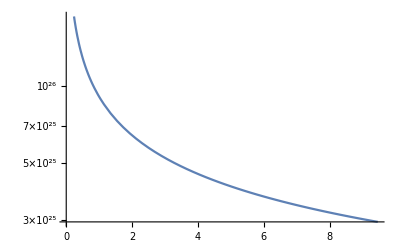

```mathematica
LogPlot[L, {t, 1 yr, 3*^6 yr }]
```

```mathematica
t=3*^6 yr;
```

```mathematica
L
```

2.9518×10^25

```mathematica
Matm/Mc
```

0.301454 A